```mathematica
figNo=1;
captionStyle={FontFamily-> "Book Antiqua", FontSize->16};
$Line=0;
```

# Chapter 49 | Supporting Notebook Artificial Neural Networks and Probability Revision 2

## Editors’ Notes

1.
Throughout this and the other Supporting Notebooks, we will have occasion to refer to the author of the Information Processing series. We feel on the one hand that repeatedly referring to our late friend as David is perhaps a little bit too personal in this context, but on the other hand referring to him as Blower seems all together too impersonal. Our compromise is to refer respectfully to the author of his unfinished volume IV as DB.

2.
In this and the other Supporting Notebooks, text—both English and Mathematica—quoted directly from Volume IV is indented in Times New Roman font, thus:

In this the other Supporting Notebooks, text—both English and Mathematica—quoted directly from Volume IV is indented in Times New Roman font, thus:

3.
Numerical values produced by DB’s Mathematica ANN code and reported in his text will almost certainly never be exactly replicated by the same code in this Notebook. This is due to the different values of the system variable $RandomState at the moment of calculation in the respective computers involved.

## Introduction

In this Supporting Notebook for Chapter 49, Artificial Neural Networks and Probability, we provide working Mathematica code reflecting as accurately as possible the code presented by David Blower in the text of his Chapter 49, Volume IV.

As discussed elsewhere (An Editors’ Apologia), this Notebook and it’s companion Supporting Notebooks will make extensive use of the functions defined in the IP package, which therefore must be called first before the rest of the code in each Notebook will execute properly. If the following Needs[] statement executes properly, this Notebook should execute without error in a running time of around 200-210 seconds.

We always recommend starting from a fresh kernel when executing a Supporting Notebook for the first time.

## Installing and Checking the IP Package

In this Supporting Notebook for Chapter 49 we include a fuller discussion and analysis of the IP package than we include in the Supporting Notebooks for Chapters 50, 51, 52, 53, and 54. We demonstrate such functions as functionListing[], functionCount[], and functionListInformation[].

In the other Supporting Notebooks we simply call Needs[“IP`”] and then functionListing[“IP`”].

If the package file IP.m has been correctly installed in the reader’s system (see the Notebook Read-Me-First.nb), the following Needs[“IP`”] statement will install the functions defined in the IP package.

```mathematica
Needs["IP`"]
```

Several of the functions in the IP package itself allow the reader to check that the functions have been installed properly. We illustrate the operation of these function only in this Section, Installing and Checking the IP Package, of this Supporting Notebook for Chapter 49, assuming that this is the first Supporting Notebook investigated by the reader. Only the preceding Needs[“IP`”] statement is included at this point in the other Supporting Notebooks.

functionListing[] outputs an alphabetically sorted list of the names of all the Package functions. Here is its Usage statement.

```mathematica
?functionListing
```

This illustrates its intended function:

```mathematica
functionListing[ "IP`" ]
```

{captionNeatFigured,cellNumberingAssociation,cellTable,cellValue,chap50MEP,codeInTextCell,codeInTextCell999,conditionalStatements,constraintFunctionAveMEP,constraintFunctionMatrix,constraintFunctionVectorF,egyptianFraction,egyptianFractionSimple,entropyH,entropyQiMEP,framedNoLabelWithCaption,functionCount,functionListInformation,functionListing,highlight,infoPrint,inputGivesOutput,interactionF,lagrangeMEP,lambdas,legendreMethod,marginalStatements,mepAlgorithm,mepAlgorithmProbabilities,mySymbolQ,myXlogX2,partitionFunctionMEP,partitionFunctionZ,probabilityQi,probPlot,qConditionalProbability,qReplace,statementSymbol,statementVector,stateSpace,twoAxisPlot}

If the reader has started with a clean Mathematica kernel, there should be no defined functions in the Global` context:

```mathematica
functionListing[]
```

{}

functionCount[] does just what you might expect:

```mathematica
?functionCount
```

```mathematica
functionCount["IP`"]
```

41

```mathematica
functionCount[]
```

0

At this point functionListInformation[] outputs the usage statements of all the Package-defined functions.

```mathematica
?functionListInformation
```

Noting that: “If a function does not have a usage statement, the function code will be listed”, this function was useful during the development of the Package, detecting defined functions without a Usage statement since the full code—no blue background—is listed rather than a usage statement. WRI strongly suggest that functions written for use in “public” Notebooks should have many of the properties and attributes of Mathematica’s own functions, including easily obtained online help.

```mathematica
(* ⌚ 5 seconds *)
functionListInformation["IP`"];
```

captionNeatFigured[captionString,charsPerLine] produces a String consisting of captionString prefixed by, e.g., ''Figure 17. '' extending when necessary over several lines.
The Figure number is automatically incremented. (figNo should be initialised Globally.)
The parameter charsPerLine governs (roughly) the number of characters per line.
Coloured words are not permitted.

cellNumberingAssociation[order] returns an Association with the mapping
of the cell numbers xi to the joint statements in the state space. And vice versa. 
The numbering is consecutively from outside-to-inside. For example in A2B2C2, A is the outermost statement
and C is the innermost, or a nesting A[B[C]].
First the C statements are traversed, then the B statements, and then the A statements.
cellNumberingAssociation[] calls statementVector[] and statementSymbol[].

cellTable[order] returns a nested List of all joint statements in the state space (with their cell numbers).
 The Mathematica Symbol order (i.e., order has Head[] Symbol) is the ordering for the joint statements.
 The function MatrixForm[] is used for the rectangular display.
cellTable[] calls cellNumberingAssociation[] and stateSpace[].

cellValue[values] returns the cell numbering and values as ''number:value'' strings.
 The function MatrixForm[] is used for the rectangular display.

chap50MEP[cfm,cfa] returns the probabilities Q_i.
cfm is the matrix of constraint functions.
cfa is a vector of contsraint values.
chap50MEP[] calls lagrangeMEP[].

codeInTextCell[text1,code,text2] produces a Text cell consisting of:
(i) the text in text1, followed by …
(ii) the *result* of executing code, followed by …
(iii) the text in text2.
For example:
codeInTextCell[ ''We refer to Figure'', (figNo),  ''below.'' ]
⟹
We refer to Figure 15 below.

Note that if the reference is to a previous rather than a following Figure, we want:
codeInTextCell[ ''We refer to Figure'', (figNo-1),  ''above.'' ]
⟹
We refer to Figure 15 above.

(Typically the variable figNo is incremented via figNo++ when each Figure's caption is generated, so must be decremented if codeInTextCell[] is called after the immediately preceding Figure).

In some Notebooks in which codeInTextCell[] is used, the Stylesheet sets the background colour of Text cells to light yellow. By setting the Background, CellFrame, and CellFrameColor options appropriately, all lines in the resulting text cell are aligned with regular text cells.
Inspiration for this function came from the StackExchange page herehttps://mathematica.stackexchange.com/questions/211225/how-to-mix-text-and-formulas-in-a-single-cell-in-the-wolfram-cloud-notebookNonehttps://mathematica.stackexchange.com/questions/211225/how-to-mix-text-and-formulas-in-a-single-cell-in-the-wolfram-cloud-notebookHyperlinkActionRecycledHyperlinkActive.

IP`codeInTextCell999

conditionalStatements[stat,cond,nemo] returns two lists {l1,l2} which comprise the conditional joint statements of stat.
  The Lists l1 and l2 hold the joint statements of the numerator and the denominator, (See Blower Eq. 42.14)
  The Mathematica Symbol nemo is the Point Nemo for the state space.
conditionalStatements[] calls marginalStatements[].

constraintFunctionAveMEP[cfm,qi] returns the constraint function averages
given by the product cfm.qi, where qi is a list of the probabilities Q_i.

constraintFunctionMatrix[order] generates a List[] of constraint function vectors based on the symbol order.
Although the function name contains the substring ''matrix'' the generated List[] is not mathematically a matrix, although it can be made to look like a matrix with MatrixForm[].
constraintFunctionMatrix[] calls statementVector[] and constraintFunctionVectorF[].

constraintFunctionVectorF[int,order] returns the constraint function vector for the interaction int (which can be a Symbol or an Integer), based on the state space based on order.
constraintFunctionVectorF[] calls interactionF[], marginalStatements[], cellNumberingAssociation[], and stateSpace[].

egyptianFraction[sr] expresses the small (signed) rational sr in the form of a signed Egyption Fraction, i.e., as 1/n for n an integer, where Abs[sr-1/n] is minimized.

egyptianFractionSimple[sr] expresses the ''small real'' sr as an Egyption Fraction of the form 1/n, n an integer.
Experimentation suggests that Round[] gives smaller mean errors than either Floor[] or Ceiling[].

entropyH[] is an overloaded function which calculates symbolic and numeric entropies, depending on the form of the input.The name ''entropyH'' was inspired by the use of the notation H(Subscript[q, 1],Subscript[q, 2],...,Subscript[q, n]) used by E.T. Jaynes in PTTLOS, Section 11.3 Entropy: Shannon's theorem, borrowing C.E. Shannon's original notation.
The units of a numeric entropy are ''nats'', since Log[] rather than Log2[] is always used in these entropy calculations.

entropyH[cfm] returns the symbolic (with the symbolic Lagrange multipliers represented as λ_i) entropy of the probabilities {Subscript[q, 1],Subscript[q, 2],...,Subscript[q, n]}, i.e., the entropy -∑ q_i Log(q_i), if cfm is a constraint function matrix.
The probabilities {Subscript[q, 1],Subscript[q, 2],...,Subscript[q, n]} are calculated using probabilityQi[cfm], and are by construction non-negative and add to 1.
entropyH[probList] returns the numerical entropy of the numerical probabilities (which must sum to 1) in the list probList.
entropyH[cfm] calls probabilityQi[cfm] only if the argument cfm is a Matrix.

entropyH[cfm,cfa] reurns the (numeric) entropy of the probabilities Subscript[q, i] derived from the (numeric) constraint function matrix cfm and the associated list of (numeric) constraint function averages vector cfa.
entropyH[cfm,cfa] calls chap50MEP[cfm,cfa].

entropyH[arg] returns the numerical entropy -∑ q_i ln(q_i) if arg is a List or Vector and consists of only numeric elements q_i and ∑ q_i == 1.
If arg is a List or Vector and consists of only numeric elements q_i and ∑ q_i != 1, an error message is returned.
If arg is not a List or Vector an error message is returned.
If arg consists of only symbolic elements, the symbolic expression
-∑ q_i ln(q_i) is returned, e.g., ''-q1 Log[q1]-q2 Log[q2]''.
If arg consists of both numeric and symbolic elements, an error message is generated.

entropyQiMEP[cfm,cfa] reurns the entropy of the probabilities Subscript[Q, i]
derived from the (numeric) constraint function matrix cfm and the associated (numeric) constraint function averages vector cfa.
entropyQiMEP[] calls chap50MEP[]

framedNoLabelWithCaption[g,caption,iSize] produces a Framed version of the graphic g, with ImageSize iSize (default 700), Print-ed so that there is no Cell Label.
g must be a graphic, usually a screenshot.
Below the Framed graphic the centred caption is rendered as ⌘-7 text.
Since a local definition of autoCollapse[] is included in framedNoCellLabel[]'s defining code, the final result is super clean, as the call to framedNoCellLabel[] is ''folded'' away and thus invisible.
Usage such as:

framedNoLabelWithCaption[ g, Style[ StringForm[StringJoin[  ''Figure `1`. '', captionNeat[ String, 12]],figNo++], captionStyle ],700 ]

will output a Framed-ed and caption-ed with:
(i) An automatically incrementing Figure number; and
(ii) the caption String produced by captionNeat[] in the (Globally defined) style captionStyle.
The second integer parameter to captionNeat[] is the required words-per-line, a mechanism designed to control the appearance of the caption text.

functionCount[context] gives a count of the symbols in the Context[] context that have nontrivial DownValues, i.e., all the user-defined functions in the Context[] context.
A nominated context - as in functionListInformation[''contextName`''] - must be the name of another Context[], i.e., whose last character is `.
functionCount[context] counts functions in the Context[] context that both do and do not have a usage statement.
The default context is ''Global`''.

functionListInformation[context] gives an alphabetic listing of all the Information[] for the symbols in the Context[] context that have nontrivial DownValues, i.e., all the user-defined functions in the Context[] context.
The default context is ''Global`''.
If a function does not have a usage statement, the function code will be listed.

functionListing[context] gives an alphabetic list of all the symbols in the Context[] context that have nontrivial DownValues, i.e., it gives a list of all the defined functions in the Context[] context.
functionListing[''IP`''] gives an alphabetic list of all the functions in the IP package.
Since the default context is ''Global`'', functionListing[] gives an alphabetic list of all the functions in the Global context. i.e., the ''locally'' defined functions.
functionListing[context] lists functions in the Context[] context that both do and do not have a usage statement.

highlight[cell,valCol] outputs the String cell (of the form, e.g., ''cellNumber:cellValue'') in the colour in the list valCol
(of the form, e.g.,  {{cellNumber, ''Red''},{cellNumber, ''Blue''},.…}) whose cellNumber matches the cellNumber in cell.
For example,
highlight''12:0.345'',{{''12'',Red},{''12'',Blue}}] ⟹ 12:0.345
whereas
highlight''11:0.345'',{{''12'',Red},{''11'',Blue}}] ⟹ 12:0.345.

infoPrint[string] is used to produce custom usage statements having italics and other font/face/size formatting combinations which do *not* adversely affect the ⌘-shift-K function  templating functionality.

inputGivesOutput[code] produces printed output of the form code ⟹ res, where res is the result of evaluating code.
If the input code is of the form var = code, the variable var is correctly assigned to the result of evaluating code.
Note that in such cases, to invoke inputGivesOutput[] using PostFix syntax, enclose the input code in parentheses:
(var = code) // inputGivesOutput.
The 2^nd last code line (''ToExpression[codeString];'')—before autoCollapse1[]—ensures that any following input using ''%'' to refers correctly to the output from code.
inputGivesOutput[] calls autoCollapseInternal[] ''internally''so that the calling Input is folded away.

interactionF[int,order] returns a Symbol for the interaction int, which can be a Symbol or an Integer.
interactionF[] calls statementVector[] and statementSymbol[].

lagrangeMEP[cfm,cfa, wp] returns the Lagrange parameters Subscript[λ, j] with precision wp, whose default value is MachinePrecision.
cfm is the matrix of constraint functions.
cfa is a vector of constraint values.
lagrangeMEP[] calls NMinimize[], in which WorkingPrecision is set to 30.

lambdas[cfm] returns a list of Symbol[]s of the form {λ1, λ2, …, λn}
corresponding to the n rows of the cfm matrix; each of the n rows is a constraint function vector cfv.

legendreMethod[cm,cfa] gives the list {p_me,λ_me} of maxent probabilities p_i and Lagrange multipliers λ_i for a problem defined by a constraint function matrix cm and an associated list of constraint function averages cfa.
Chop[…, 10^-10] is applied to the λ_me to avoid silly small numbers.
A series of Print[]s reports a number of intermediate quantities, in particular the symbolic and numeric partition function Z and the maximum entropy H.
legendreMethod[] calls NMinimize[ …, WorkingPrecision→30]

marginalStatements[stat,nemo] returns a list of joint statements which comprise the marginal sum of stat.
  The Mathematica Symbol nemo is the Point Nemo for the state space.
  marginalStatements[stat,nemo] returns an empty List {} when the joint statement stat is not in the state space nemo.
marginalStatements[] calls stateSpace[] and statementVector[].

mepAlgorithm[cm,cfa], given a List of constraint function averages (cfa) and a matrix (actually a list of lists of constraint function coedfficients masquerading as a matrix, cm), outputs a labelled list of its internal variables, both diagnostic and those of external interest, such as the Maximum Entropy probabilities (in real and rational forms), the corresponding entropy, the partition function (symbolic and numerical), and a ''check'' calculation of the input cfa.

mepAlgorithmProbabilities[cm, cfa],given a List of constraint function averages (cfa) and a matrix (actually a list of lists of constraint function coedfficients masquerading as a matrix, cm), outputs, a list of the Maximum Entropy probabilities (as reals).

mySymbolQ[x] returms True if Head[x] is Symbol or Subscript, and returns False otherwise.

myXlogX2[p] returns the numerical value of p Log[p] if NumberQ[p] is True, otherwise a symbolic expression such as ''p1 Log[p1]''.
If p=0 or p=0.0, 0 is returned.

partitionFunctionMEP[cfm,cfa] returns the value of the partition function 𝒵
based on the constraint function matrix cfm and the associated constraint function averages cfa.
partitionFunctionMEP[] calls lagrangeMEP[].

partitionFunctionZ[cvm] returns the sum ∑_(j = 1)^n Exp[λ_j.cfm], where n is the number of rows of cvm.
partitionFunctionZ[] calls lambdas[].

probabilityQi[cfm] returns a list of the (symbolic) probabilities Q_i
corresponding to the constraint function matrix (i.e., matrix of constraint function vectors) cfm. 
The symbolic Lagrange multipliers are represented as λ_i.
probabilityQi[] calls lambdas[] and partitionFunctionZ[].

probPlot[{l_,u_},{params__},dist_] produces a (captioned) plot of the PDF of the distribution dist with parameters params, together with a shaded region under the PDF curve representing the integral from l to u.
Sensible l and u limits determine a sensible interval over which the PDF is plotted.
The numerical value of the integral is displayed beside the PDF curve, as is the distribution with its parameters.

qConditionalProbability[stat,cond,order] returns the conditional probability of stat conditioned on cond, as the ratio of Qi Symbols. For example qConditionalProbability[C1,A1B1,A2B2C2]  returns Q1/(Q1+Q2).
 The ordering of statements in order defines the cell numbers Qi.
qConditionalProbability[] calls conditionalStatements[] and cellNumberingAssociation[].

qReplace[qi,subscript] creates a list of replacement rules {Q1->qi[[1]],Q2->qi[[2]],...} (default,subscript:False),
or with subscripted symbols {Q_1->qi[[1]],Q_2->qi[[2]],...} (subscript:True).

statementSymbol[join] returns a Mathematica Symbol.
For instance, statementSymbol[{A3,B2,C1}] returns the symbol A3B2C1.
The symbols in the list join are concatenated (in alphabetical order) into a single Symbol.

statementVector[stat] returns a sorted List. For example statementVector[A3B2C1] is returned as {A3,B2,C1}. 
  The expression A3B2C1 is an elementary point in the State Space (Blower Ch. 13.2.1).
  The statement stat is a Mathematica Symbol, being the conjunction of one or more single letter-digit pairs.

stateSpace[nemo] returns a sorted List of all joint statements in the state space.
 The Mathematica Symbol nemo is the Point Nemo for the joint statements.
The elementary statements are sorted alphabetically.

twoAxisPlot[{f_,g_},{x_,x1_,x2_},opts:OptionsPattern[]] plots the functions f and g together over the interval from x1 to x2 but with different vertical axes.
Each plot is fully scaled, with the left FrameTicks relating to f (in the matching blue colour RGBColor[0.24720000000000014, 0.24, 0.6]) and the right FrameTicks relating to g (in the matching colour dark red RGBColor[0.6, 0.24, 0.4428931686004542]).
The PlotLegends are also in the matching colours.

## Artificial Neural Networks and Probability: Motivation

As noted in our Editor’s Apologia, DB included two Chapters in Volume III introducing Artificial Neural Networks (ANNs) into his treatment of Information Processing. These were Chapter 42 Boltzmann Machines, and Chapter 43 Hidden Units for Boltzmann Machines.

At the beginning of Chapter 42 DB introduces Boltzmann Machines as follows:

Boltzmann machines provide us with an opportunity to discuss how certain general inferential problems often have unique, traditional, and perhaps, to some extent, accidental histories attached to them. These kind of contingent histories are quite understandable whenever a problem has been studied on its own merits over a long period of time.
	The topic of artificial neural networks (ANNs) presents us with one such class of inferential problems which have experienced a unique history. At first glance, ANNs appear to be somewhat detached from the conceptual underpinnings and the jargon that I have tried to associate with inference as a generalization of logic. Swimming against the tide, I would like instead to emphasize the commonalities shared by all inferential problems rather than their differences due to some particular contingent and accidental history.

The Introduction to Chapter 43 begins:

Let’s return to the theme of some contingent history associated with artificial neural networks. A by–product of such an accidental history is a certain idiosyncratic way of thinking about problems, together with an associated terminology and notation. I am going to couch the discussion in this Chapter by employing the Boltzmann machine’s own unique Gestalt as it formed outside of the separate and distinct contingent history that gave rise to general inferencing.
	Thus, this Chapter will tend to frame inferential explanations in terms of some neural network architecture, consisting of input units, hidden units, and output units. The input units and output units are labeled as visible units because they correspond to known observables in the real world, while the hidden units are latent variables created for the sole purpose of revealing some hidden pattern or structure not readily perceivable in the input units. The hidden units and output units are activated through weights connecting the units.
	The input units are activated when environmental variables are clamped to the input units, which then in turn feed into activation of hidden units, and finally into the activation of output units. These output units are supposed to represent any target variables. This propagation is an asynchronous dynamic affair with each activation a momentary fleeting thing awaiting the next round of new activations. All of the weights connecting two units undergo a continuous change that depends on a gradient.
The main question here is the following: Will the introduction of hidden units help the Boltzmann machine overcome the impediment of relying on models with information solely from double interactions?

We let these two quotations from Chapters 42 and 43 respectively stand as some motivation for the whole of Volume IV, and proceed to implement and in some cases Expand on the Mathematica  code included in Chapter 49.

```mathematica
$Line=0;
```

## 49.1 Introduction

No Mathematica  code.

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, page 1.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 1. Screenshot from Volume IV, page 1.

## 49.2 Review of the Probabilistic Solution

No Mathematica  code.

$Line = $Line-2;
framedNoLabelWithCaption[ , Style[ StringForm[captionNeatFigured[ "Figure 49.1 from Volume IV, page 3.", 112  ],figNo++], captionStyle ],500 ]

-Graphics-
Figure 2. Figure 49.1 from Volume IV, page 3.

This call to cellTable[] does NOT produce a table that agrees with DB’s Figure 49.1:

```mathematica
cellTable[A2B2]
```

(1:A1B1 | 2:A1B2
3:A2B1 | 4:A2B2)

```mathematica
?cellTable
```

This call to cellTable[] DOES agree with DB’s Figure 49.1:

```mathematica
cellTable[A2B2]
```

(1:A1B1 | 2:A1B2
3:A2B1 | 4:A2B2)

This call to cellValue[] returns the probabilities in the appropriate cells.

```mathematica
cellValue[{{1/3,1/3},{0,1/3}}]
```

(1:1/3 | 2:1/3
3:0 | 4:1/3)

```mathematica
?cellValue
```

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, Chapter 49, page 5.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 3. Screenshot from Volume IV, Chapter 49, page 5.

```mathematica
cfm49=
{
   {1,0,1,0}   (* cells 1 and 3 for A is true *)
      ,{1,1,0,0}   (* cells 1 and 2 for B is True *)
      ,{1,0,0,0}   (* cell 1 for AB is True *) 
}; 
MatrixForm[%]
```

(1 | 0 | 1 | 0
1 | 1 | 0 | 0
1 | 0 | 0 | 0)

```mathematica
{Subscript[λ, 1],Subscript[λ, 2],Subscript[λ, 3]}.cfm49
```

{λ_1+λ_2+λ_3,λ_2,λ_1,0}

These are the constraint function averages (cfa):

```mathematica
cfa49={1/3,2/3,1/3}
```

{1/3,2/3,1/3}

```mathematica
?lagrangeMEP
```

These are the Lagrange parameters:

```mathematica
lagrangeMEP[cfm49,cfa49]
```

{-32.483020756207,0,32.483020756207}

```mathematica
?chap50MEP
```

These are the probabilities:

```mathematica
qi49=chap50MEP[cfm49,cfa49]
qi49//Chop//Rationalize
```

{0.333333,0.333333,2.60425×10^-15,0.333333}

{1/3,1/3,0,1/3}

```mathematica
?constraintFunctionAveMEP
```

These are the constraint function averages:

```mathematica
constraintFunctionAveMEP[cfm49,qi49]
%//Rationalize
```

{0.333333,0.666667,0.333333}

{1/3,2/3,1/3}

These should also return the constraint function averages:

```mathematica
cfm49.qi49
%//Rationalize
```

{0.333333,0.666667,0.333333}

{1/3,2/3,1/3}

```mathematica
?partitionFunctionMEP
```

This is the partition function value :

```mathematica
partitionFunctionMEP[cfm49,cfa49]
%//Rationalize
```

3.

3

## 49.3 The Multilayer Perceptron

No Mathematica  code.

$Line = $Line-2;
framedNoLabelWithCaption[ , Style[ StringForm[captionNeatFigured[ "Figure 49.2 from Volume IV, page 7.", 112  ],figNo++], captionStyle ],400 ]

-Graphics-
Figure 4. Figure 49.2 from Volume IV, page 7.

lineNumber=$Line;

a1=.
a2=.
Graph[
{x->h_1,a_1->h_1
  ,x->h_2,a_2->h_2
  ,h_1->f_1,b_1->f_1,h_2->f_1
  ,h_1->f_2,h_2->f_2,b_2->f_2
},
VertexLabels→Automatic,
GraphLayout->"SpringElectricalEmbedding"]//Framed;

Labeled[ %, Style[ StringForm["Figure `1` . The structure of the multilayer perceptron 
 in Figure 49.2 rendered by Graph[] with
GraphLayout -> ''SpringElectricalEmbedding''.",figNo++], captionStyle ] ]//Print

$Line=lineNumber-2;

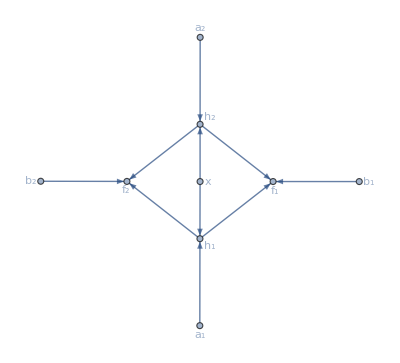
-Graphics-Figure 5 . The structure of the multilayer perceptron 
 in Figure 49.2 rendered by Graph[] with
GraphLayout -> ''SpringElectricalEmbedding''.

## 49.4 Mathematica Approach to a Solution for the Multilayer Perceptron

No Mathematica  code.

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Figure 49.2 from Volume IV, page 8.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 6. Figure 49.2 from Volume IV, page 8.

### 49.4.1 Define the architecture

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Figure 49.2 from Volume IV, page 9.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 7. Figure 49.2 from Volume IV, page 9.

```mathematica
net=NetChain[{LinearLayer[2],ElementwiseLayer[Tanh],LinearLayer[2],SoftmaxLayer[]}
  ,"Input"->1
  ,"Output"->2
  ]
```

NetChain[<>]

(Click the “+“ sign in the preceding output to see the full structure of net.)

There are several ways to display the structure of the neural net, net.

Click the “+“ sign and either of the -Graphics- and  -Graphics- icons in the following output to see the full structure of net.

```mathematica
NetGraph[net]
```

NetGraph[<>]

Information about the structure of the network can be obtained in various ways; here are a few examples:

```mathematica
Information[net]
```

Net Information

```mathematica
net//Normal
```

{LinearLayer[<>],ElementwiseLayer[<>],LinearLayer[<>],SoftmaxLayer[<>]}

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Figure 49.2 from Volume IV, page 9.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 8. Figure 49.2 from Volume IV, page 9.

```mathematica
net = NetChain[{LinearLayer[2],ElementwiseLayer[Tanh],LinearLayer[2],SoftmaxLayer[]}
  ,"Input"->"Scalar"
  ,"Output"->2
  ]
```

NetChain[<>]

Again, clicking on the “+“ signs in the preceding output shows the full structure of net, with the input layer at  the bottom and the output layer at the top of the diagram.

### 49.4.2 Train the defined network

DB could have explained the following training data in slightly more detail by adding that training the network that if B is FALSE then P(A) = 0 requires training it so that the input vector {2} for B is associated with the output vector {0,1}, since the output vector is {P(A),P(Ā)}.

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, page 10.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 9. Screenshot from Volume IV, page 10.

```mathematica
(* ⌚ ~20 seconds *)
trained=.
trained=NetTrain[net,{1->{0.5,0.5},1->{0.5,0.5},2->{0,1},2->{0,1}}
  ,LossFunction->CrossEntropyLossLayer["Probabilities"]
]
```

NetChain[<>]

trained =.
trained = NetTrain[net, {{1} -> {0.5, 0.5}, {1} -> {0.5, 0.5}, {2} -> {1, 0}, {2} -> {1, 0}}
    , LossFunction -> CrossEntropyLossLayer["Probabilities"]
  ]

Again, clicking on the “+“ signs in this output shows the full structure of net.

```mathematica
NetGraph[trained]
```

NetGraph[<>]

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, page 10.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 10. Screenshot from Volume IV, page 10.

In our case, trained[1] and its log_10 are …

```mathematica
trained[1]
Log10[ trained[1] ]
```

{0.499966,0.500034}

{-0.30106,-0.301}

The argument “2” in trained[2] is the value of B???!!!

RB:
Should  P (Ā | B = 1) be  P (A | B = 2) in Figure 8? And consequently, shouldn’t DB’s reported output for trained[2] be something like {~0, ~1}? , as in …

```mathematica
trained[2]
Log10[ trained[2] ]
```

{0.0000339604,0.999966}

{-4.46903,-0.0000147553}

```mathematica
trained[{3}]
```

{{7.28225×10^-6,0.999993}}

```mathematica
trained[{0}]
Log10[ trained[{0}] ]
```

{{0.999196,0.000804475}}

{{-0.000349524,-3.09449}}

After all, in DB’s Figure 49.2 (our Figure 4), B (or not B) is the input to the network, and thus is the conditioning statement!?

ListPlot[ {Map[ (s |-> {s, trained[s][[1]]}), Table[in, {in, 0, 2, 0.025}] ], Map[ (s |-> {s, trained[s][[2]]}), Table[in, {in, 0, 2, 0.025}] ]}, ...]

lineNumber=$Line;

ListPlot[ {Map[ (s↦{s, trained[s]⟦1⟧}), Table[in,{in, 0, 2, 0.025}] ],Map[ (s↦{s, trained[s]⟦2⟧}), Table[in,{in, 0, 2, 0.025}] ]}, ImageSize->400,PlotRange→{-0.05, 1.05},Frame→True, FrameLabel→{"Value of input B","Output values"}, PlotLegends→{"Ouput A","Output ¬A"}]//Framed;

Labeled[ %, Style[ StringForm[captionNeatFigured[ "This shows the output from ''trained''—given only 2 instances of {1}→{0.5,0.5} and 2 instances of {2}→{0,1}—for a range of input ''B'' values. The truth function effectively synthesised by the network ''extrapolates'' to smaller numerical values of the input in an obvious way.", 67  ],figNo++], captionStyle ] ]//Print

$Line=lineNumber-2;

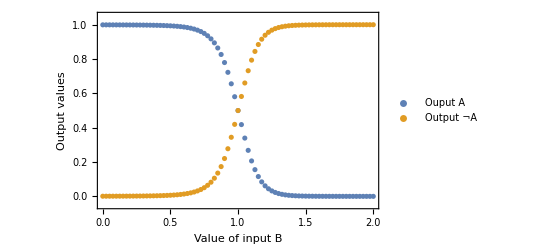
-Graphics-Figure 11. This shows the output from ''trained''—given only 2
instances of {1}→{0.5,0.5} and 2 instances of {2}→{0,1}—for a range of
input ''B'' values. The truth function effectively synthesised by
the network ''extrapolates'' to smaller numerical values of the
input in an obvious way.

We insert here an illustration of the effect of more training data; now the network is trained with 100 instances of B being TRUE and 100 instances of B being FALSE.

```mathematica
(* ⌚ ~40 seconds *)
trained=.
trained=NetTrain[net,
Table[ 1->{0.5,0.5}, 100 ]~Join~Table[ 2->{0,1}, 100 ]
  ,LossFunction->CrossEntropyLossLayer["Probabilities"]
]
```

NetChain[<>]

The reproduction of the training probabilities is now even more faithful.

```mathematica
trained[1]
Log10[ trained[1] ]
```

{0.499989,0.500011}

{-0.301039,-0.301021}

```mathematica
trained[2]
Log10[ trained[2] ]
```

{7.26426×10^-7,0.999999}

{-6.13881,-3.10632×10^-7}

```mathematica
trained[{3}]
```

{{1.24484×10^-7,1.}}

```mathematica
trained[{0}]
Log10[ trained[{0}] ]
```

{{0.999955,0.0000454858}}

{{-0.0000197514,-4.34212}}

lineNumber=$Line;

ListPlot[ {Map[ (s↦{s, trained[s]⟦1⟧}), Table[in,{in, 0, 2, 0.025}] ],Map[ (s↦{s, trained[s]⟦2⟧}), Table[in,{in, 0, 2, 0.025}] ]}, ImageSize->400,PlotRange→{-0.05, 1.05},Frame→True, FrameLabel→{"Value of input B","Output values"}, PlotLegends→{"Ouput A","Output ¬A"}]//Framed;

Labeled[ %, Style[ StringForm[captionNeatFigured[ "This shows the output from ''trained'' given 200 samples, with 100 instances of {1}→{0.5,0.5} and 100 instances of {2}→{0,1}. The truth function again effectively synthesised by the network ''extrapolates'' to smaller values of the input in an obvious way.", 70  ],figNo++], captionStyle ] ]//Print

$Line=lineNumber-2;

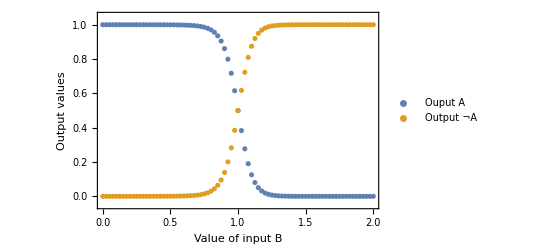
-Graphics-Figure 12. This shows the output from ''trained'' given 200 samples,
with 100 instances of {1}→{0.5,0.5} and 100 instances of {2}→{0,1}.
The truth function again effectively synthesised by the network
''extrapolates'' to smaller values of the input in an obvious way.

### 49.4.3 Shorter version

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, page 10.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 13. Screenshot from Volume IV, page 10.

```mathematica
net2 = NetChain[{2, Tanh, 2, SoftmaxLayer[ ]}, "Input"->"Scalar"]
```

NetChain[<>]

### 49.4.4 Longer version (Use of Association)

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, page 10.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 14. Screenshot from Volume IV, page 10.

```mathematica
(* Note that in this code, DB uses ""Input"→1 rather than "Input"→Scalar *)
net3=NetInitialize@NetChain[<|
        "layer1"->LinearLayer[2]
       ,"layer2"->ElementwiseLayer[Tanh]
       ,"layer3"->LinearLayer[2]
       ,"layer4"->SoftmaxLayer[]|>
       ,"Input"->1
       ,"Output"->2
]
```

NetChain[<>]

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, page 11.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 15. Screenshot from Volume IV, page 11.

```mathematica
(* ⌚ ~20 seconds *)
(* note now the form of the training data: {1}->{0.5,0.5}, rather than 1->{0.5,0.5} *)
trained3=NetTrain[net3,{{1}->{0.5,0.5},{1}->{0.5,0.5},{2}->{0,1},{2}->{0,1}}
  ,LossFunction->CrossEntropyLossLayer["Probabilities"]
]
```

NetChain[<>]

RB:
Learned a trick here. Can’t have arrows with hyperlinks to tagged cells in code. Trick is, enclose them within a
(* comment *).

```mathematica
trained3[{1}]
trained3[{2}] (*  ↓from500068  ↓from500068#2 *)
```

{0.499868,0.500132}

{0.00020142,0.999799}

Our output here is inconsistent with DB’s “trained3[{2}] giving {0.0077, 0.9923}”, as quoted immediately above.

lineNumber=$Line;

ListPlot[ {Map[ (s↦{s, trained3[s]⟦1⟧}), Table[in,{in, 0, 2, 0.025}] ],Map[ (s↦{s, trained[s]⟦2⟧}), Table[in,{in, 0, 2, 0.025}] ]}, ImageSize->400,PlotRange→{-0.05, 1.05},Frame→True, FrameLabel→{"Value of input B","Output values"}, PlotLegends→{"Ouput A","Output ¬A"}]//Framed;

Labeled[ %, Style[ StringForm[captionNeatFigured[ "This shows the output from ''trained3'' given 2 instances of {1}→{0.5,0.5} and 2 instances of {2}→{0,1}. The truth function effectively synthesised by the network ''extrapolates'' to smaller values of the input in an obvious way.", 70  ],figNo++], captionStyle ] ]//Print

$Line=lineNumber-2;

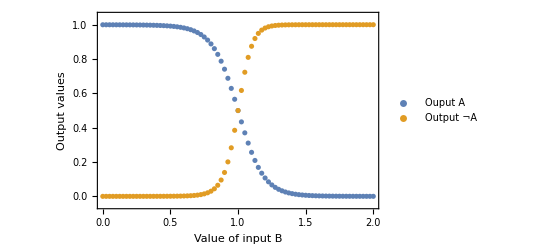
-Graphics-Figure 16. This shows the output from ''trained3'' given 2 instances
of {1}→{0.5,0.5} and 2 instances of {2}→{0,1}. The truth function
effectively synthesised by the network ''extrapolates'' to smaller values
of the input in an obvious way.

NetExtract[] can retrieve the Biases and Weights from a trained network:

```mathematica
Normal @ NetExtract[trained3,{"layer1","Biases"}]
Normal @ NetExtract[trained3,{"layer1","Weights"}]
```

{-0.570052,1.19264}

{{0.734752},{-1.07296}}

These values are rather different from DB’s values (p. 14)

Third layer : {b_1,b_2} and {{v_11,v_21},{v_12,v_22}}   (Note the unusual order of the indices.)

```mathematica
Normal@NetExtract[trained3,{"layer3","Biases"}]
Normal@NetExtract[trained3,{"layer3","Weights"}]
```

{-0.0943438,0.0943442}

{{-1.68096,3.69654},{2.44756,-3.54115}}

```mathematica
Transpose@Normal@NetExtract[trained3,{"layer1","Weights"}]
```

{{0.734752,-1.07296}}

Input True=1 and False=2 into the first layer:

```mathematica
(* True = 1 *)
Dot[{1},Transpose@Normal@NetExtract[trained3,{"layer1","Weights"}]]
(* False = 2 *)
Dot[{2},Transpose@Normal@NetExtract[trained3,{"layer1","Weights"}]]
```

{0.734752,-1.07296}

{1.4695,-2.14593}

### 49.4.5 Relationship to MEP

No Mathematica  code.

## 49.5 Connections to the Literature

No Mathematica  code.

## 49.6 Solved Exercises for Chapter Forty Nine

### Exercise 49.6.1: Write out the full expansion of the functions at the two output nodes.

No Mathematica  code.

It will be convenient to have DB’s sketch of a multilayer perceptron.

$Line = $Line-2;
framedNoLabelWithCaption[ , Style[ StringForm[captionNeatFigured[ "Figure 49.2 from Volume IV, page 7.", 112  ],figNo++], captionStyle ],400 ]

-Graphics-
Figure 17. Figure 49.2 from Volume IV, page 7.

The solution to Exercise 49.6.1 begins:

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 13.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 18. Screenshot from Chapter 49, page 13.

Then follows:

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 13.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 19. Screenshot from Chapter 49, page 13.

Here we bring forward some calculations from the “next exercise”, so as to be able the check the calculations for Exercise 49.5.1.

```mathematica
{a1,a2}=Normal@NetExtract[trained3,{"layer1","Biases"}]  
{{u11},{u12}}=Normal@NetExtract[trained3,{"layer1","Weights"}]
```

{-0.570052,1.19264}

{{0.734752},{-1.07296}}

Linear equations in layer 1:

```mathematica
{u11*x+a1,u12*x+a2}/.x->1
{u11*x+a1,u12*x+a2}/.x->2
```

{0.1647,0.119673}

{0.899452,-0.953291}

Tanh[] function in layer 2:

```mathematica
Tanh[{u11*x+a1,u12*x+a2}/.x->1]
Tanh[{u11*x+a1,u12*x+a2}/.x->2]
```

{0.163227,0.119105}

{0.716031,-0.741269}

Combine the functions in h_1 and h_2:

```mathematica
ClearAll[h1,h2]

h1[x_]:=Tanh[u11*x+a1]  (* hidden node 1 *)
h2[x_]:=Tanh[u12*x+a2]  (* hidden node 2 *)

{h1[1],h2[1]}  (* True *)
{h1[2],h2[2]}      (* False *)
```

{0.163227,0.119105}

{0.716031,-0.741269}

Layer 3 : {b_1,b_2} and {{v_11,v_12},{v_21,v_22}}. (Note the extra Normal[] function extracting numerical values.)

```mathematica
{b1,b2}=Normal@NetExtract[trained3,{"layer3","Biases"}]
{{v11,v12},{v21,v22}}=Transpose@Normal@NetExtract[trained3,{"layer3","Weights"}]
```

{-0.0943438,0.0943442}

{{-1.68096,2.44756},{3.69654,-3.54115}}

The full functions:

```mathematica
ClearAll[f1,f2]

f1[x_]:=b1+v11*h1[x]+v21*h2[x]
f2[x_]:=b2+v12*h1[x]+v22*h2[x]

(* True *)
{f1[1],f2[1]} 
(* False *){f1[2],f2[2]}
```

{0.0715552,0.072082}

{-4.0381,4.47181}

Finally, Layer 4: the Softmax[] layer using the Exp[], gives (and see below) …

```mathematica
Exp[{f1[1],f2[1]}]/Total@Exp[{f1[1],f2[1]}]
Exp[{f1[2],f2[2]}]/Total@Exp[{f1[2],f2[2]}]
```

{0.499868,0.500132}

{0.00020142,0.999799}

Note that these last two lists of probabilities correspond to these.

The following Inputs set out the detailed calculations behind inputs such as trained3[{1}] and trained3[{2}]:

```mathematica
ClearAll[output]
output[input_]:= 
  Exp[
    Dot[
      Tanh[
        Dot[{input},Transpose@Normal@NetExtract[trained3, {"layer1", "Weights"}]] 
        + Normal@NetExtract[trained3, {"layer1", "Biases"}]
      ]
      ,Transpose@Normal@NetExtract[trained3, {"layer3", "Weights"}] ]
    + Normal@NetExtract[trained3, {"layer3", "Biases"}]
  ]
```

```mathematica
output[1]
output[2]
```

{1.07418,1.07474}

{0.0176309,87.5153}

After normalization we get

```mathematica
{output[1][[1]] / (output[1][[1]] + output[1][[2]])
,output[1][[2]] / (output[1][[1]] + output[1][[2]])}
```

{0.499868,0.500132}

```mathematica
{output[2][[1]] / (output[2][[1]] + output[2][[2]])
,output[2][[2]] / (output[2][[1]] + output[2][[2]])}
```

{0.00020142,0.999799}

Compare these values with the earlier results from trained3[]:

```mathematica
trained3[{1}]
trained3[{2}]
```

{0.499868,0.500132}

{0.00020142,0.999799}

This is satisfactory agreement; the differences are …

```mathematica
{output[1][[1]] / (output[1][[1]] + output[1][[2]])
,output[1][[2]] / (output[1][[1]] + output[1][[2]])} - trained3[{1}]
```

{3.48446×10^-9,-3.48446×10^-9}

… and …

```mathematica
{output[2][[1]] / (output[2][[1]] + output[2][[2]])
,output[2][[2]] / (output[2][[1]] + output[2][[2]])}- trained3[{2}]
```

{4.94668×10^-11,-1.62457×10^-8}

### Exercise 49.6.2: Confirm the numerical values for the probability at the two output nodes of the first simple multilayer perceptron through independent Mathematica calculations.

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 14.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 20. Screenshot from Chapter 49, page 14.

It is convenient to assign some variables to the results of these calculations:

```mathematica
{a1,a2}=Normal@NetExtract[trained3,{"layer1","Biases"}]
```

{-0.570052,1.19264}

```mathematica
{{u11},{u12}} = Normal@NetExtract[trained3,{"layer1","Weights"}]
```

{{0.734752},{-1.07296}}

The  Explicit calculations corresponding to Exercise 49.5.1 are …

```mathematica
Tanh[ a1 + u11 × 1 ]
```

0.163227

… and …

```mathematica
Tanh[ a2 + u12 × 1 ]
```

0.119105

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 15.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 21. Screenshot from Chapter 49, page 15.

```mathematica
Tanh[Dot[{1},Transpose[Normal@NetExtract[trained3,{"layer1","Weights"}]]]+Normal@NetExtract[trained3,{"layer1","Biases"}]]
```

{0.163227,0.119105}

Or …

```mathematica
Tanh[Dot[{1},Transpose[{{u11},{u12}}]]+{a1,a2}]
```

{0.163227,0.119105}

(Note that these are the two values calculated above via Tanh[a1+u11×1]and Tanh[a2+u12×1] respectively.)

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 15.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 22. Screenshot from Chapter 49, page 15.

```mathematica
Normal@NetExtract[trained3, {"layer3", "Biases"}]
```

{-0.0943438,0.0943442}

```mathematica
Normal@NetExtract[trained3, {"layer3", "Weights"}]
```

{{-1.68096,3.69654},{2.44756,-3.54115}}

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 15.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 23. Screenshot from Chapter 49, page 15.

```mathematica
Dot[ Tanh[Dot[{1},Transpose[Normal@NetExtract[trained3,{"layer1","Weights"}]]]+Normal@NetExtract[trained3,{"layer1","Biases"}]],
  Transpose[Normal@NetExtract[trained3, {"layer3", "Weights"}] ] +
  Normal@NetExtract[trained3, {"layer3", "Biases"}] ]
```

{0.161736,-0.0264247}

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 15.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 24. Screenshot from Chapter 49, page 15.

```mathematica
output[input_ ] := Exp[ Dot[ Tanh[ Dot[{input}, Transpose[Normal@NetExtract[trained3, {"layer1", "Weights"}]] ] +
      Normal@NetExtract[trained3, {"layer1", "Biases"}] ], Transpose[Normal@NetExtract[trained3, {"layer3", "Weights"}]] ] +
   Normal@NetExtract[trained3, {"layer3", "Biases"}] ]
```

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 16.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 25. Screenshot from Chapter 49, page 16.

```mathematica
NetExtract[trained3, {"layer1", "Weights"}]//Normal
NetExtract[trained3, {"layer1", "Biases"}]//Normal
NetExtract[trained3, {"layer3", "Weights"}]//Normal
NetExtract[trained3, {"layer3", "Biases"}]//Normal
```

{{0.734752},{-1.07296}}

{-0.570052,1.19264}

{{-1.68096,3.69654},{2.44756,-3.54115}}

{-0.0943438,0.0943442}

```mathematica
output[1][[1]] / Total[output[1]]
```

0.499868

```mathematica
output[2][[1]] / Total[output[2]]
```

0.00020142

Recall from above …

```mathematica
trained3[{1}]
```

{0.499868,0.500132}

… and …

```mathematica
trained3[{2}]
```

{0.00020142,0.999799}

… or more completely …

```mathematica
{output[1][[1]] / Total[output[1]],output[1][[2]] / Total[output[1]]}
```

{0.499868,0.500132}

… and …

```mathematica
{output[2][[1]] / Total[output[2]],output[2][[2]] / Total[output[2]]}
```

{0.00020142,0.999799}

Again, these last two lists of probabilities agree with those here.

### Exercise 49.6.3: Show the explicit calculations being conducted at the SoftmaxLayer[ ] when viewed through the lens of the MEP formula.

(See also below our Editors’ Discussion of Exercise 49.6.3.)

No Mathematica  code.

We note that earlier, on page 12, DB says:
“SoftmaxLayer[] must be computing a conditional probability P (A | B, ℳ_k), not a joint probability P(A, B | ℳ_k). However, the Q_i produced via the MEP formula are numerical assignments to joint probabilities.”

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 12.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 26. Screenshot from Chapter 49, page 12.

DB begins his Solution to Exercise 49.6.3 by writing out the conditional probability “…  produced at the first output node A when the input node B is fixed at a value of 1 …” in terms of Bayes’ Theorem:

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 16.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 27. Screenshot from Chapter 49, page 16.

This equation first appears, in exactly this form, on page 2, in Section 49.2, Review of the Probabilistic Solution.
Next, DB relates the two probabilities in this expression to probabilities obtained via the MEP.

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 16.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 28. Screenshot from Chapter 49, page 16.

At this stage a particular framework for an application of the MEP is missing. DB explicitly says: “The … probabilities appearing in the numerator and denominator of Bayes’s Theorem have the MEP representations, …” (emphasis added).

Now DB says: “Suppose one were to think of the three λ_j parameters as the two weights and the one bias emanating from the hidden layer to the output layer.” (emphasis added)

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 16.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 29. Screenshot from Chapter 49, page 16.

The data {{1}→ {.5, .5}, {{1}→ {.5, .5}, {{2}→ {0, 1}, {{2}→ {0, 1}} are simulating the set of equations (actually twice):

P(A_1|B_1)=(P(A_1,B_1))/(P(B_1))=Q_1/(Q_1+Q_2)=0.5
P(A_2|B_1)=(P(A_2,B_1))/(P(B_1))=Q_2/(Q_1+Q_2)=0.5
P(A_1|B_2)=(P(A_1,B_2))/(P(B_2))=Q_3/(Q_3+Q_4)=0
P(A_2|B_2)=(P(A_2,B_2))/(P(B_2))=Q_4/(Q_3+Q_4)=1

From this we immediately see that Q_3=0, and we are left with

Q_1+Q_2+Q_4=1

We have an underdetermined set of equations, for which we can obtain the range of allowed values via Reduce[]:

```mathematica
Reduce[
  {q1/(q1+q2)==1/2
     ,q2/(q1+q2)==1/2
,q3/(q3+q4)==0
,q4/(q3+q4)==1
     ,q1+q2+q3+q4==1
     ,0≤q1≤1
     ,0≤q2≤1
,0≤q3≤1
     ,0≤q4≤1
  }
  ,
  {q1,q2,q3,q4}
  ,Reals
]
```

0<q1<1/2&&q2==q1&&q3==0&&q4==1-q1-q2

Here we plot q1, q2 (=q1, with a small numerical separation for clarity), and q4 (= 1-2q1), together with the entropy H(q1,q2,q4) as a function of the free variable q1, noting that …

```mathematica
entropyH[  {q1,q2,q4} ]
```

-q1 Log[q1]-q2 Log[q2]-q4 Log[q4]

… so that, using the result from Reduce[] above the entropy expression is …

```mathematica
entropyH[  {q1,q2,q4} ]//.{q2->q1, q4->1-q1-q2}
```

-((1-2 q1) Log[1-2 q1])-2 q1 Log[q1]

gr=Plot[ {q1, q1+0.025, 1-2q1, -((1-2 q1) Log[1-2 q1])-2 q1 Log[q1]},  {q1, 0,1/2}, PlotLegends->"Expressions", Frame->True ];
Labeled[ gr, Style[ StringForm[captionNeatFigured[ "q1 (blue), q2 (orange), and q4 (green) with H(q1,q2,q4) (red).", 140  ],figNo++], captionStyle ] ]//Print

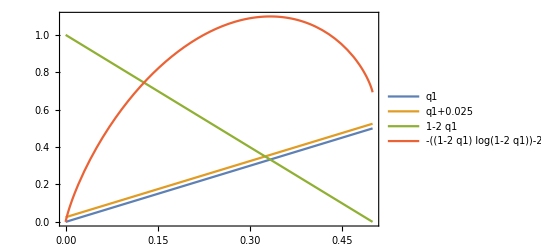
-Graphics-Figure 30. q1 (blue), q2 (orange), and q4 (green) with H(q1,q2,q4) (red).

FindMaximum[] (with rational constants) gives the numerical value of q1 giving the maximum entropy:

```mathematica
FindMaximum[ {-((1-2 q1) Log[1-2 q1])-2 q1 Log[q1], 0≤q1≤1/2}, {q1, 1/23} ]
```

{1.09861,{q1→0.333334}}

Maximize[] (with rational constants) gives the exact value of q1 giving the (exact) maximum entropy:

```mathematica
Maximize[ {-((1-2 q1) Log[1-2 q1])-2 q1 Log[q1], 0≤q1≤1/2}, {q1} ]
```

{Log[3],{q1→1/3}}

By invoking the MEP as an extra principle, we can obtain a unique solution to this set of equations. Since q3==0, we need only solve for q1, q2, and q4. (This observation helps us avoids the troublesome evaluation of 0 Log[0].)

```mathematica
Maximize[
  {-q1 Log[q1]-q2 Log[q2]-q4 Log[q4]  (* entropy *)
  ,0<q1<1/2&&q2==q1&&q4==1-q1-q2 (* conditions *)
  }
  ,
  {q1,q2,q4}
]
```

{Log[3],{q1→q2,q2→1/3,q4→1/3}}

Note that the full solution  {1/3, 1/3, 0, 1/3}, including the q3=0, agrees with the “Implies” model A→B.

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 16.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 31. Screenshot from Chapter 49, page 16.

Where do these numbers come from?
We copy the reported numerical values from page 13:

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 13.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 32. Screenshot from Chapter 49, page 13.

```mathematica
{a1,a2}={1.84612,0.02466};
{u11,u12}={−1.47458,−0.60991};
```

Calculation h_1(1) and h_2(2) …

```mathematica
{h1[x],h2[x]}
{h1[1],h2[1]}
```

{Tanh[1.84612-1.47458 x],Tanh[0.02466-0.60991 x]}

{0.355338,-0.526471}

… gives DB’s reported values almost exactly. (See our comment below on entering numerical values into Mathematica typed exactly as they appear.)

Copying the reported numerical values from page 14:

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 14.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 33. Screenshot from Chapter 49, page 14.

(Note that the slightly more precise values 0.753114 for v_21 and −0.0865838 for v_22 we use here are from pages 16 and 17 respectively.)

```mathematica
{b1,b2}={−0.492303,0.492303};
{{v11,v12},{v21,v22}}={{1.73319,−2.22651},{0.753114,−0.0865838}};
```

```mathematica
{b1,b2}={−0.492303,0.492303};
{{v11,v12},{v21,v22}}={{1.73319,−2.22637},{0.753114,−0.0865838}};
```

DB’s values for f_1(1) and f_2(1) are—in this case--exactly reproduced:

```mathematica
{f1[x],f2[x]}
{f1[1],f2[1]}
```

{-0.492303+1.73319 Tanh[1.84612-1.47458 x]+0.753114 Tanh[0.02466-0.60991 x],0.492303-2.22637 Tanh[1.84612-1.47458 x]-0.0865838 Tanh[0.02466-0.60991 x]}

{-0.272927,-0.253227}

Opening the calculation of f1[1] to full scrutiny, we have:

```mathematica
f1[x]
```

-0.492303+1.73319 Tanh[1.84612-1.47458 x]+0.753114 Tanh[0.02466-0.60991 x]

Since …

```mathematica
Tanh[1.84612-1.47458 1]
```

0.355338

… and …

```mathematica
Tanh[0.02466-0.60991 1]
```

-0.526471

… the expanded calculation gives …

```mathematica
-0.492303+1.73319 Tanh[1.84612-1.47458 1]+0.753114` Tanh[0.02466-0.60991 1]
```

-0.272927

Note that entering numerical values into Mathematica typed exactly as they appear in a printed text gives values whose Precision is only what is “visible”:

```mathematica
{Rationalize[b1,0], Rationalize[b2,0]}
```

{-492303/1000000,492303/1000000}

Compare this “rational equivalent” calculation:

```mathematica
Exp[5.0]/1000
```

0.148413

Behind the displayed 6 significant figures there is a number with more precision:

```mathematica
Exp[5.]/1000//FullForm
```

0.148413

Thus Exp[5.0]/1000 is not equal to 148413/1000000…

```mathematica
Exp[5.0]/1000-148413/1000000
```

1.59103×10^-7

… whereas 0.492303 is 492303/1000000 …

```mathematica
0.492303 - 492303/1000000
```

0.

Arithmetic and Exponential calculations with “typed in reported” quantities will therefore not necessarily exactly duplicate reported resulting calculations.

For clarity we repeat the earlier screenshot from page 16:

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 16.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 34. Screenshot from Chapter 49, page 16.

Equating, as suggested, the λ’s with the two weights and the bias term …

```mathematica
{λ1,λ2,λ3}={v11,v21,b1}  (* set 1 *)
```

{1.73319,0.753114,-0.492303}

… and …

```mathematica
h1[1]
```

0.355338

```mathematica
{f1x1,f2x1,f3x1}={h1[1],h2[1],1}
```

{0.355338,-0.526471,1}

… the Exponential expression for the numerator of  Q_1—calculated either way—gives …

```mathematica
Exp[{λ1,λ2,λ3}.{f1x1,f2x1,f3x1}]
Exp[{v11,v21,b1}.{h1[1],h2[1],1}]
```

0.761148

0.761148

DB’s reported value is 0.761147. Taking this as the “true” value, our % error is …

```mathematica
(Exp[{λ1,λ2,λ3}.{f1x1,f2x1,f3x1}] - 0.761147)/0.761147 100. "%"
```

0.000153918 %

DB continues with this idea:

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 17.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 35. Screenshot from Chapter 49, page 17.

Again equating, as suggested, λ’s with weights and a bias term ……

```mathematica
{λ1,λ2,λ3}={v12,v22,b2}  (* set 2 *)
{h1[1],h2[1],1}
```

{-2.22637,-0.0865838,0.492303}

{0.355338,-0.526471,1}

(Note: The value of v_12 we use here, -2.22637, is copied from the page 17 screenshot above, where, in addition, v_22 is given the more precise value -0.0865838.
The value of v_12 given on page 14 is -2.22651, along with the less precise value for v_22, -0.08658.)

… the Exponential expression calculated either way gives …

```mathematica
Exp[{λ1,λ2,λ3}.{f1x1,f2x1,f3x1}]
Exp[{v12,v22,b2}.{h1[1],h2[1],1}]
```

0.776292

0.776292

Within the limitations of the use of reported quantities entered as they appear into Mathematica, these values are convincing conformations of DB’s values.

Continuing …

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 17.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 36. Screenshot from Chapter 49, page 17.

The consequent probabilities are …

```mathematica
Exp[{v11,v21,b1}.{h1[1],h2[1],1}]/(Exp[{v11,v21,b1}.{h1[1],h2[1],1}]+Exp[{v12,v22,b2}.{h1[1],h2[1],1}])
```

0.495075

… and …

```mathematica
Exp[{v12,v22,b2}.{h1[1],h2[1],1}]/(Exp[{v11,v21,b1}.{h1[1],h2[1],1}]+Exp[{v12,v22,b2}.{h1[1],h2[1],1}])
```

0.504925

And they sum to unity:

```mathematica
%% + %
```

1.

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 17.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 37. Screenshot from Chapter 49, page 17.

Using DB’s reported values gives the corresponding values …

```mathematica
Exp[{v11,v21,b1}.{h1[2],h2[2],1}]
Exp[{v12,v22,b2}.{h1[2],h2[2],1}]
```

0.0814042

10.475

… and the corresponding probabilities are …

```mathematica
Exp[{v11,v21,b1}.{h1[2],h2[2],1}]/(Exp[{v11,v21,b1}.{h1[2],h2[2],1}]+Exp[{v12,v22,b2}.{h1[2],h2[2],1}])
```

0.00771138

```mathematica
Exp[{v12,v22,b2}.{h1[2],h2[2],1}]/(Exp[{v11,v21,b1}.{h1[2],h2[2],1}]+Exp[{v12,v22,b2}.{h1[2],h2[2],1}])
```

0.992289

And they also sum to unity:

```mathematica
%% + %
```

1.

Earlier we quoted DB’s values as:

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 16.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 38. Screenshot from Chapter 49, page 16.

We now see these quoted values—0.495074 and 0.0077114—reproduced almost perfectly, by using weights and biases reported in DB’s text, derived from his ANN calculations with his random number seed settings. Using our random number seed settings, we obtain values …

```mathematica
output[1]⟦1⟧ / Total[ output[1] ]
```

0.499868

```mathematica
output[2]⟦1⟧ / Total[ output[2] ]
```

0.00020142

… that are numerically different but qualitatively equivalent to those  obtained by DB.

Finally:

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 17.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 39. Screenshot from Chapter 49, page 17.

```mathematica
{Subscript[λ, 1], Subscript[λ, 2], Subscript[λ, 3]} = lagrangeMEP[cfm49,cfa49]
```

{-32.483020756207,0,32.483020756207}

```mathematica
ⅇ^Subscript[λ, 2]/(ⅇ^Subscript[λ, 2]+ⅇ^Subscript[λ, 2])
```

1/2

… and …

```mathematica
ⅇ^Subscript[λ, 1]/(ⅇ^Subscript[λ, 1]+ⅇ^Subscript[λ, 2])
```

7.8127392508598×10^-15

### Editors’ Discussion of Exercise 49.6.3 (↑)

On page 16 DB suggests:
“Suppose one were to think of the three λ_j parameters as the two weights and the one bias emanating from the hidden layer to the output layer. Likewise, think of the F_j(X = x_i) constraint functions as the two values at the hidden layer nodes plus the fixed value of 1 for the bias term, in order to calculate the numerator according to the MEP formula …”.

RB and BJS are of the view that this key idea behind Exercise 49.6.3 is misguided. One can certainly make the formal association between (a vector of) Lagrange Multiplier λ’s and (a vector of) weights and biases, and form the dot product with (a list of) some the constraint function (values) and a “fixed value of 1”.

Why is this association justified? Does it generalize? What is its deeper meaning?

One of us (RB) has analysed the idea this way:

The generic form of the Lagrange parameters is
(λ_1,λ_2,λ_3)=(w_1,w_2,b_1)

and the constraint function matrix is
F_j(X=x_i)=(h_11 | h_12 | h_13 | h_14
h_21 | h_22 | h_23 | h_24
1 | 1 | 1 | 1) for j=1,2,3  and i=1,2,3,4

Just by counting the unknowns, we have three Lagrange multipliers (λ_1,λ_2,λ_3) and eight unknown coefficients in the constraints F_j(X=x_i).

These eleven variables have to be matched with the network graph on page 7:

$Line = $Line-2;
framedNoLabelWithCaption[ , Style[ StringForm[captionNeatFigured[ "Figure 49.2 from Volume IV, page 7.", 112  ],figNo++], captionStyle ],400 ]

-Graphics-
Figure 40. Figure 49.2 from Volume IV, page 7.

graph is topologically equivalent to that in DB’s Figure 49.2:

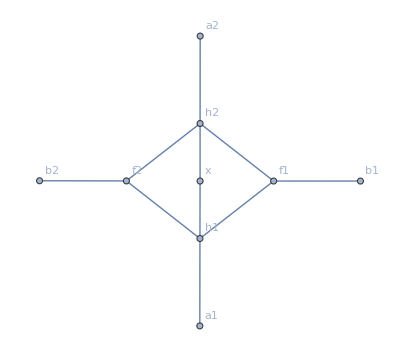

```mathematica
graph=Module[{a1="a1",a2="a2",b1="b1",b2="b2",f1="f1",f2="f2",h1="h1",h2="h2",x="x"},
  Graph[{x<->h1,a1<->h1
    ,x<->h2,a2<->h2
    ,h1<->f1,b1<->f1,h2<->f1
    ,h1<->f2,h2<->f2,b2<->f2
                       
  },VertexLabels->Automatic]
]
```

Mathematica gives …

```mathematica
EdgeCount[graph]
VertexCount[graph]
```

10

9

```mathematica
ClearAll[ h1,h2, u11,u12, a1, a2,f1,f2,v11,v12,v21,v22,b1,b2 ]
h1[x_]:=Tanh[u11*x+a1]  (* hidden node 1 *)
h2[x_]:=Tanh[u12*x+a2]  (* hidden node 2 *)
```

```mathematica
h1[x]
h2[x]
```

Tanh[a1+u11 x]

Tanh[a2+u12 x]

```mathematica
f1[x_]:=b1+v11*h1[x]+v21*h2[x]
f2[x_]:=b2+v12*h1[x]+v22*h2[x]
```

```mathematica
f1[x]
f2[x]
```

b1+v11 Tanh[a1+u11 x]+v21 Tanh[a2+u12 x]

b2+v12 Tanh[a1+u11 x]+v22 Tanh[a2+u12 x]

By inspection, parameter count for each of the functions f1[] and f2[] is 7.

This illustrates the operation of the SoftMax[] layer producing the output probabilities.
softmax is a SoftmaxLayer[] layer taking 2 inputs:

```mathematica
softmax=SoftmaxLayer["Input"->{2}]
```

SoftmaxLayer[<>]

Given the 2 inputs {1,2} it gives …

```mathematica
softmax[{1,2}]
```

{0.268941,0.731059}

… via the underlying calculation …

```mathematica
ⅇ^{1,2}/Total[  ⅇ^{1,2}]
ⅇ^{1,2}/Total[  ⅇ^{1,2}]//N
```

{ⅇ/(ⅇ+ⅇ^2),ⅇ^2/(ⅇ+ⅇ^2)}

{0.268941,0.731059}

This last symbolic output makes the formal similarity of the SoftmaxLayer[] and MEP calculations in this case clear.

```mathematica
ⅇ^{f1[x],f2[x]}/Total[  ⅇ^{f1[x],f2[x]}]
```

{ⅇ^(b1+v11 Tanh[a1+u11 x]+v21 Tanh[a2+u12 x])/(ⅇ^(b1+v11 Tanh[a1+u11 x]+v21 Tanh[a2+u12 x])+ⅇ^(b2+v12 Tanh[a1+u11 x]+v22 Tanh[a2+u12 x])),ⅇ^(b2+v12 Tanh[a1+u11 x]+v22 Tanh[a2+u12 x])/(ⅇ^(b1+v11 Tanh[a1+u11 x]+v21 Tanh[a2+u12 x])+ⅇ^(b2+v12 Tanh[a1+u11 x]+v22 Tanh[a2+u12 x]))}

This makes clear the inspiration for the idea behind Exercise 49.6.3.

$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 12.", 112  ],figNo++], captionStyle ],600 ]

-Graphics-
Figure 41. Screenshot from Chapter 49, page 12.

Redefining each of f1[] and f2[] as functions of the values at the nodes of the hidden layer, say, 𝒽1 and 𝒽2, …

```mathematica
f1[x_]:=b1+v11*𝒽1+v21*𝒽2
f2[x_]:=b2+v12*𝒽1+v22*𝒽2
```

… we have for the probabilities …

```mathematica
ⅇ^{f1[x],f2[x]}/Total[  ⅇ^{f1[x],f2[x]}]
```

{ⅇ^(b1+v11 𝒽1+v21 𝒽2)/(ⅇ^(b1+v11 𝒽1+v21 𝒽2)+ⅇ^(b2+v12 𝒽1+v22 𝒽2)),ⅇ^(b2+v12 𝒽1+v22 𝒽2)/(ⅇ^(b1+v11 𝒽1+v21 𝒽2)+ⅇ^(b2+v12 𝒽1+v22 𝒽2))}

```mathematica
{Subscript[λ, 11], Subscript[λ, 12], Subscript[λ, 13]} = {v11, v21, b1}
```

{v11,v21,b1}

```mathematica
{Subscript[λ, 21],Subscript[λ, 22],Subscript[λ, 23]}={v12,v22,b2}
```

{v12,v22,b2}

The two dot products proposed by DB are …

```mathematica
{Subscript[λ, 11],Subscript[λ, 12],Subscript[λ, 13]}.{𝒽1,𝒽2,1}
{Subscript[λ, 21],Subscript[λ, 22],Subscript[λ, 23]}.{𝒽1,𝒽2,1}
```

b1+v11 𝒽1+v21 𝒽2

b2+v12 𝒽1+v22 𝒽2

… so that the probabilities calculated as per the MEP formula are …

```mathematica
{ⅇ^({Subscript[λ, 11], Subscript[λ, 12], Subscript[λ, 13]}.{𝒽1,𝒽2,1})/(ⅇ^({Subscript[λ, 11], Subscript[λ, 12], Subscript[λ, 13]}.{𝒽1,𝒽2,1})+ⅇ^({Subscript[λ, 21],Subscript[λ, 22],Subscript[λ, 23]}.{𝒽1,𝒽2,1})),ⅇ^({Subscript[λ, 21],Subscript[λ, 22],Subscript[λ, 23]}.{𝒽1,𝒽2,1})/(ⅇ^({Subscript[λ, 11], Subscript[λ, 12], Subscript[λ, 13]}.{𝒽1,𝒽2,1})+ⅇ^({Subscript[λ, 21],Subscript[λ, 22],Subscript[λ, 23]}.{𝒽1,𝒽2,1}))}
```

{ⅇ^(b1+v11 𝒽1+v21 𝒽2)/(ⅇ^(b1+v11 𝒽1+v21 𝒽2)+ⅇ^(b2+v12 𝒽1+v22 𝒽2)),ⅇ^(b2+v12 𝒽1+v22 𝒽2)/(ⅇ^(b1+v11 𝒽1+v21 𝒽2)+ⅇ^(b2+v12 𝒽1+v22 𝒽2))}

… which is also …

```mathematica
ⅇ^{f1[x],f2[x]}/Total[  ⅇ^{f1[x],f2[x]}]
```

{ⅇ^(b1+v11 𝒽1+v21 𝒽2)/(ⅇ^(b1+v11 𝒽1+v21 𝒽2)+ⅇ^(b2+v12 𝒽1+v22 𝒽2)),ⅇ^(b2+v12 𝒽1+v22 𝒽2)/(ⅇ^(b1+v11 𝒽1+v21 𝒽2)+ⅇ^(b2+v12 𝒽1+v22 𝒽2))}

```mathematica
%%-%
```

{0,0}

This is all very well if the ANN has as many nodes in the last hidden layer as there are λ’s in the MEP formulation, but it appears to us that this is not generally necessarily the case.

Notice also that we have had to introduce two sets of λ’s, one for each output probability. As the expression in the above screenshot shows, there is only one set of λ’s in the MEP formulation; the j^th probability is proportional to the vector of λ’s “dotted” with the j^th column of the constraint function matrix.

We finish this discussion of DB’s idea with some notes we made while pondering it.

This equating of {λ1,λ2,λ3} with {v11,v21,b1} is not given any mathematical justification, other than that the MEP formula is then seen to imitate the ANN calculations.
Is this generally true?
DB doesn’t assert this or its opposite.

We think that what generally motivated David to start Volume IV was a basic desire to see what connections could be made between Probability Theory (PT) on the one hand and Artificial Neural Networks (ANNs) on the other. As is well known, ANNs can be persuaded to give “probabilities” associated with the possible classifications they generate.

These “probabilities” however, are not based on Probability Theory, but are based on interpreting a set of weights, or figures of merit, or scores, and convert these to  “probabilities” via normalization.
It is our (RB and BJS) opinion that this practice is conceptually wrong.

It seems that perhaps in this Exercise 49.6.3 David was trying to show some mathematical connection of this kind.

From the WDC for SoftmaxLayer[]:
“SoftmaxLayerpaclet:ref/SoftmaxLayer is typically used inside NetChainpaclet:ref/NetChain, NetGraphpaclet:ref/NetGraph, etc. to normalize the output of other layers in order to use them as class probabilities for classification tasks. “

We emphasise “… in order to use them as class probabilities  …”
They are not probabilities calculated by any model that incorporates any part of Probability Theory. We contend that therefore they are not true probabilities.

The moral of this story could be, to paraphrase von Neumann’s “Anyone who considers arithmetical methods of producing random digits is, of course, in a state of sin” that “Anyone who considers a normalised list of positive numbers as a list of probabilities is, of course, in a state of sin.”

## A Further Note: RB on Random Seed Initialization

Different runs give different outcomes due to the random initializations of the weights matrices. The biases are all initialized to 0.0 (see below).
Here is a mechanism to set the random seed : RandomSeeding→1

```mathematica
testNet=NetInitialize[
  NetChain[<|
        "layer1"->LinearLayer[2]
       ,"layer2"->ElementwiseLayer[Tanh]
       ,"layer3"->LinearLayer[2]
       ,"layer4"->SoftmaxLayer[]|>
       ,"Input"->1
       ,"Output"->2
  ]
  ,RandomSeeding->1
]
```

NetChain[<>]

```mathematica
(* ⌚ ~20 seconds *)trainedTestNet=NetTrain[testNet,{{1}->{0.5,0.5},{1}->{0.5,0.5},{2}->{0,1},{2}->{0,1}}
  ,LossFunction->CrossEntropyLossLayer["Probabilities"]
]
```

NetChain[<>]

```mathematica
trainedTestNet[{1}]  (* B is True *)
trainedTestNet[{2}]  (* B is False *)
```

{0.499962,0.500038}

{0.0000525966,0.999947}

With setting the random seed, the results are exactly reproduced. Here are my test values:

Test RandomSeeding→1

{0.499915,0.500085}

{0.000355683,0.999644}

Test RandomSeeding→0

{0.499987,0.500013}

{0.0000324856,0.999967}

The initialization of the ANN can be extracted.
The biases are all set to 0.0. The weights appear to be random values. 
Note that these values have been set prior to the seeing any data!

```mathematica
Normal@NetExtract[testNet,{"layer1","Biases"}]
Normal@NetExtract[testNet,{"layer3","Biases"}]

Normal@NetExtract[testNet,{"layer1","Weights"}]
Normal@NetExtract[testNet,{"layer3","Weights"}]
```

{0.,0.}

{0.,0.}

{{0.485679},{0.40914}}

{{0.185178,0.449479},{1.09198,0.478574}}

DB returns to the initialization of biases and weights in a later Chapter.